# Učení RBF sítě Demonstrace pokrytí vstupních dat RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, která obsahují několik dobře oddělených shluků dat.
Vygenerujeme náhodně tyto data.

```mathematica
values=10;
cluster1x =RandomReal[{7,6},{values,1}];cluster1y=RandomReal[ {11,12},{values,1}];
cluster2x =RandomReal[{-4,-5},{values,1}];cluster2y=RandomReal[ {9,10},{values,1}];
cluster3x =RandomReal[{0,-1},{values,1}];cluster3y=RandomReal[ {12,13},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
inDataClass1 = Join[cluster1,cluster2,cluster3];
cluster4x =RandomReal[{2,1},{values,1}];cluster4y=RandomReal[ {4,5},{values,1}];
cluster5x =RandomReal[{-3,-4},{values,1}];cluster5y=RandomReal[ {12,13},{values,1}];
cluster6x =RandomReal[{9,8},{values,1}];cluster6y=RandomReal[ {10,9},{values,1}];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inDataClass2 = Join[cluster4,cluster5,cluster6];
inData= Join[inDataClass1,inDataClass2];
outClass1=ConstantArray[{1,0},{3*values}];outClass2 = ConstantArray[{0,1},{3*values}];
outData= Join[outClass1,outClass2];
```

Takto vypadají naše vynerovaná vstupní data.

```mathematica
inData
```

{{6.71882,11.163},{6.20518,11.7673},{6.14884,11.7906},{6.46366,11.145},{6.39796,11.5068},{6.67831,11.8923},{6.87965,11.2536},{6.77711,11.0547},{6.70062,11.9531},{6.1562,11.4725},{-4.29062,9.16749},{-4.09193,9.84802},{-4.79958,9.23313},{-4.20797,9.3419},{-4.90371,9.58064},{-4.89687,9.79145},{-4.2987,9.39873},{-4.40777,9.63205},{-4.38498,9.37984},{-4.53327,9.75303},{-0.335116,12.6877},{-0.131281,12.3836},{-0.681107,12.3477},{-0.908271,12.5147},{-0.655484,12.2186},{-0.800001,12.6728},{-0.645804,12.4116},{-0.345175,12.4153},{-0.111199,12.1866},{-0.499102,12.0849},{1.43504,4.54882},{1.89051,4.59375},{1.54501,4.35048},{1.25711,4.77809},{1.97561,4.51127},{1.71279,4.49836},{1.68512,4.68858},{1.24436,4.35847},{1.78812,4.43001},{1.9781,4.52677},{-3.77398,12.9877},{-3.41118,12.7976},{-3.42522,12.1774},{-3.26861,12.5725},{-3.30188,12.0855},{-3.25737,12.3501},{-3.44216,12.2955},{-3.94655,12.9797},{-3.53204,12.0653},{-3.17064,12.3798},{8.53903,9.61079},{8.49668,9.09308},{8.82537,9.64237},{8.61204,9.33164},{8.07101,9.86444},{8.08001,9.41038},{8.81584,9.43464},{8.51111,9.12396},{8.24997,9.4947},{8.67962,9.63795}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme zobrazit pro lepší představu zobrazit. Každá třída dat má v grafu jinou bavu.

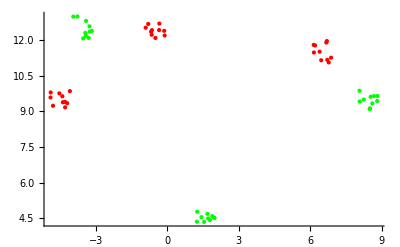

```mathematica
ListPlot[{inDataClass1,inDataClass2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě se třemi RBF neurony, dvěma vstupy a dvěma výstupy.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,3,LinearPart->False,OutputNonlinearity->Sigmoid]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 21, 18, 2, 9.9697324}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme chtěli.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-21 at 18:02. The network has 2 inputs and 2 outputs.  It consists of 3 basis functions of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

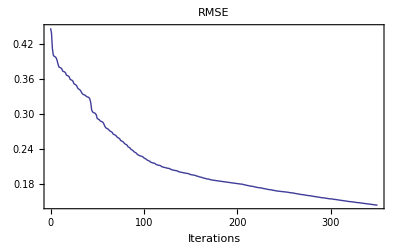

```mathematica
{net2,record}=NeuralFit[net,inData,outData,350,ReportFrequency->20];
```

Podívejme se jak naše síť klasifikuje data.

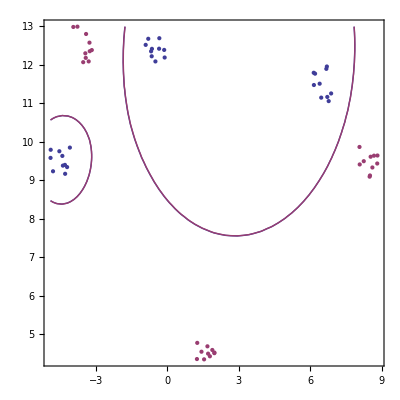

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronů

Nyní se podíváme na “vnitřnosti” neuronové sítě. Naše síť obsahuje jeden RBF neuron, mohlo by být zajímavé zjistit jakou oblast dat tento neuron pokrývá.
Nejprve upravíme síť aby vracela námi požadovaný výstup.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[3],{0,0,0}];(*změna matice vah na identickou matici*)
(*net3=NeuronDelete[net3,{0,0}];*)(*odstranění lineární části*)
```

A zobrazíme výstup.

```mathematica
gauss1=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All];
gauss2=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All];
gauss3=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All];
Show[gauss1,gauss2,gauss3]
```

-Graphics3D-

Ještě přidáme do grafu vstupní data pro lepší představu o jejich pokrytí.

```mathematica
inDataClass13d=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
inDataClass23d=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
gauss0O=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss1O=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss2O=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
data3d=ListPointPlot3D[{inDataClass13d,inDataClass23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gauss0O,gauss1O,gauss2O,data3d]
```

-Graphics3D-

Ještě se podívejme jak naučená síť klasifikuje datový prostor.

```mathematica
out1=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
inDataClass13d2=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
inDataClass23d2=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
data3d2=ListPointPlot3D[{inDataClass13d2,inDataClass23d2},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
out1true=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Red,Thick]];
Show[out1,out1true,data3d2]
```

-Graphics3D-

```mathematica
out2true=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Red,Thick],Mesh->None];
out2=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
Show[out2true,out2,data3d2]
```

-Graphics3D-

```mathematica
Show[out1true,out2true]
```

-Graphics3D-